```mathematica
<<"C:\\Users\\LukinLab\\My Documents\\Ruffin\\Dropbox\\Harvard Physics\\Lukin Lab\\Scripts and Programs\\Transmission Spectra\\Clean Code\\SpectraFitting.m"
```

Usage Instructions:

1. Get a list of spectra from a directory by using the GetSpecDir[path] function.

2. (Optional) Get an individual spectrum for flatfield correction using the GetSpec[path] function. Divide each spectrum by this flat-field using the SpecDivide[spec,ffspec] function.

3. Initialize a list of guesses using the CoordInit[Spectra,center,d] function, where center is a very preliminary guess for the center point of a generic spectrum and d is the overall spread to zoom in on for further fitting. You should save this guess as a variable.

4. Use the PickGuesses[Spectra,CoordList] command to interactively refine these guesses. CoordList should be the variable you defined in the previous step.

5. Run SingleLorentzianFit[Spectra, Coordlist] to fit each function to a single Lorentzian. Save the output to a variable. More options are coming soon.

6. Use the ShowFits[Spectra, CoordList, Fits, Path] where Fits is the list of fits and Path is the original directory to display all of the fits and important parameters.


If you need additional help, all of the functions have usage instructions that can be queried with two question marks and the name of the function, e.g. ??ShowFits .

Location of XPS excel file.

```mathematica
XPSPath="C:\\Users\\LukinLab\\My Documents\\Ruffin\\Dropbox\\Harvard Physics\\Lukin Lab\\Scripts and Programs\\Transmission Spectra\\Clean Code\\Example Data\\XPS\\2014-06-17_10048_76_77_79_synchotronsamples.xlsx";
```

## Fitting Example Data

### Example 1: Sample carbon 1s edge

First, generate some fake data from example peak positions for a carbon 1s edge:

0.0036 ⅇ^(-5.55556 (-2.3+x)^2)+0.0036 ⅇ^(-5.55556 (-1.2+x)^2)+0.3249 ⅇ^(-5.55556 x^2)+0.0441 ⅇ^(-5.55556 (0.9+x)^2)+0.01 ⅇ^(-5.55556 (1.8+x)^2)

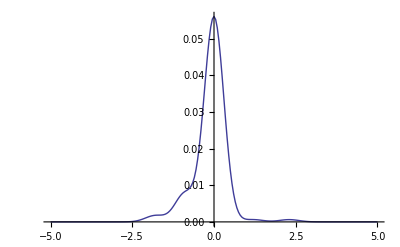

```mathematica
exweights={.10,.21,.57,.06,.06}^2; (*A^2 values, then plug in A values below*)
expositions={-1.8,-0.9,0,1.2,2.3};
ExampleCFn[x_]:=Table[gfn[Sqrt[exweights[[i]]],expositions[[i]],0.3,x],{i,1,Length[exweights]}]//Total
Print[ExampleCFn[x]]
ExampleCData=CenterAndNormalize@Table[{x,ExampleCFn[x]+0*RandomReal[]},{x,-5,5,0.05}];
ListLinePlot[ExampleCData,PlotRange->{{-5,5},All}]
```

Try to fit this data with default values. It does a pretty good job, but misses the distinction between the peak at 1.2 and 2.3 eV.

Sum of squares of residuals: 1.1726286627450673e-6

Weights | Means | σs
0.296549 | -0.000301554 | -0.298856
0.00818885 | 1.57938 | 0.930722
0.645244 | -6.33644 | -0.229521
0.0410215 | -0.897706 | 0.303995
0.00899625 | -1.80639 | 0.295501

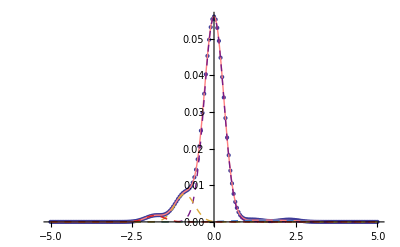

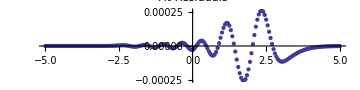

```mathematica
ExCModel=Model[ExampleCData,5];
FitSummary[ExampleCData,ExCModel];
```

Perfect results can be obtained by lowering the scaling factor.

Sum of squares of residuals: 5.433734029701012e-16

Weights | Means | σs
0.114189 | -0.9 | 0.299999
0.00932161 | 2.3 | -0.3
0.0258934 | -1.8 | -0.3
0.00932155 | 1.2 | -0.299998
0.841274 | -5.53112×10^-8 | -0.3

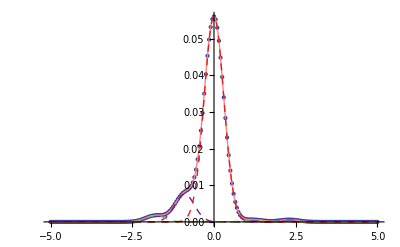

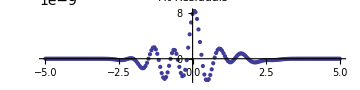

```mathematica
ExCModel=Model[ExampleCData,5,0.75];
FitSummary[ExampleCData,ExCModel];
```

### Example 2: Sample carbon 1s edge with broader peaks

Broaden the peaks from example 1. The data appears to be much harder to fit!

0.0036 ⅇ^(-3.125 (-2.3+x)^2)+0.0036 ⅇ^(-3.125 (-1.2+x)^2)+0.3249 ⅇ^(-3.125 x^2)+0.0441 ⅇ^(-3.125 (0.9+x)^2)+0.01 ⅇ^(-3.125 (1.8+x)^2)

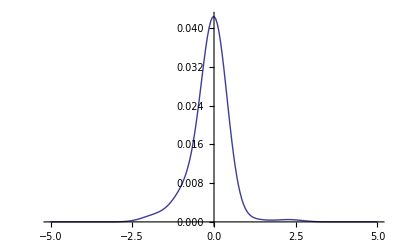

```mathematica
exweights={.10,.21,.57,.06,.06}^2; (*A^2 values, then plug in A values below*)
expositions={-1.8,-0.9,0,1.2,2.3};
ExampleCFn[x_]:=Table[gfn[Sqrt[exweights[[i]]],expositions[[i]],0.4,x],{i,1,Length[exweights]}]//Total
Print[ExampleCFn[x]]
ExampleCData=CenterAndNormalize@Table[{x,ExampleCFn[x]+0*RandomReal[]},{x,-5,5,0.05}];
ListLinePlot[ExampleCData,PlotRange->{{-5,5},All}]
```

Try to fit this data with default values. It does a pretty good job, but misses the distinction between the peak at 1.2 and 2.3 eV.

Sum of squares of residuals: 1.8697928940161893e-6

Weights | Means | σs
0.0138919 | -0.604531 | 0.645208
0.00346009 | 0.0789347 | 1.70922
0.937601 | -6.87647 | -0.325678
0.0450467 | 0.0163255 | 0.38633
7.10714×10^-16 | 1.44734 | 4.14948

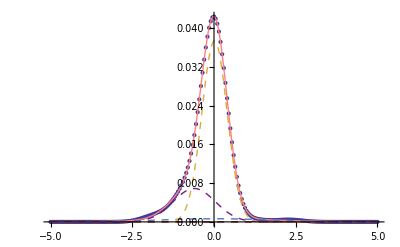

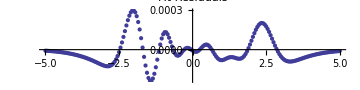

```mathematica
ExCModel=Model[ExampleCData,5];
FitSummary[ExampleCData,ExCModel];
```

Here, decreasing the scaling factor again produces a better fit that exactly reproduces the data.

Sum of squares of residuals: 1.0129166568079173e-7

Weights | Means | σs
0.0049994 | -1.01341 | -0.223818
0.68531 | 0.0163286 | 0.382365
0.00982687 | -1.98676 | -0.32746
0.2871 | -0.450779 | 0.690348
0.0127639 | 2.12781 | 0.559793

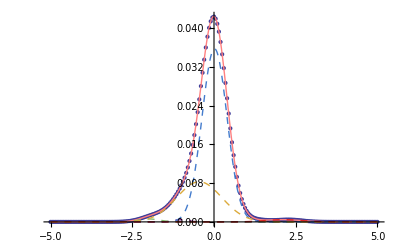

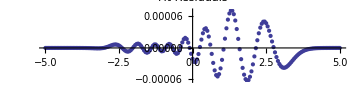

```mathematica
ExCModel=Model[ExampleCData,5,0.65];
FitSummary[ExampleCData,ExCModel];
```

### Example 3: Sample carbon 1s edge with narrower peaks

Make the peaks in example 1 more narrow.

0.0036 ⅇ^(-12.5 (-2.3+x)^2)+0.0036 ⅇ^(-12.5 (-1.2+x)^2)+0.3249 ⅇ^(-12.5 x^2)+0.0441 ⅇ^(-12.5 (0.9+x)^2)+0.01 ⅇ^(-12.5 (1.8+x)^2)

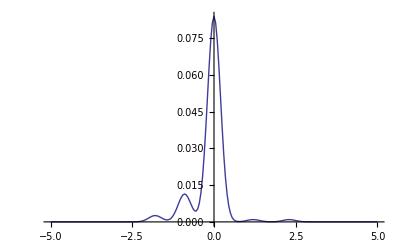

```mathematica
exweights={.10,.21,.57,.06,.06}^2; (*A^2 values, then plug in A values below*)
expositions={-1.8,-0.9,0,1.2,2.3};
ExampleCFn[x_]:=Table[gfn[Sqrt[exweights[[i]]],expositions[[i]],0.2,x],{i,1,Length[exweights]}]//Total
Print[ExampleCFn[x]]
ExampleCData=CenterAndNormalize@Table[{x,ExampleCFn[x]+0*RandomReal[]},{x,-5,5,0.05}];
ListLinePlot[ExampleCData,PlotRange->{{-5,5},All}]
```

Again, the default values do an OK job, but miss the higher energy peaks:

Sum of squares of residuals: 4.756865249060735e-6

Weights | Means | σs
0.114094 | -0.899957 | 0.200167
0.0211987 | 1.69745 | 0.829156
3.82969×10^-8 | -6.69536 | 1.72406
0.838852 | -0.000210575 | 0.199695
0.0258551 | -1.80009 | 0.199857

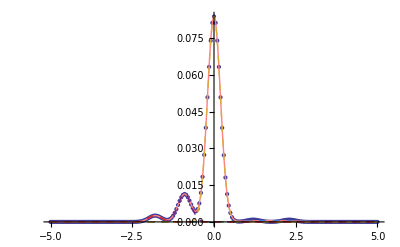

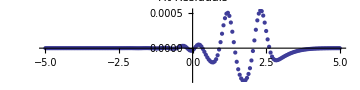

```mathematica
ExCModel=Model[ExampleCData,5];
FitSummary[ExampleCData,ExCModel];
```

Again, decreasing the scaling factor slightly gets precisely the correct result. Althoug it seems as if the choice of scaling factor should be more robust in this case, it does not appear to be.

Sum of squares of residuals: 1.4952663458090157e-15

Weights | Means | σs
0.0093216 | 1.2 | 0.200001
0.841274 | -8.13229×10^-9 | -0.2
0.0258933 | -1.8 | -0.2
0.00932164 | 2.3 | 0.200002
0.11419 | -0.9 | 0.2

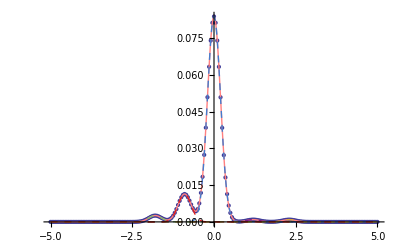

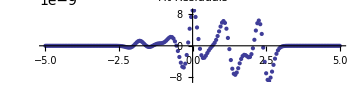

```mathematica
ExCModel=Model[ExampleCData,5,0.65];
FitSummary[ExampleCData,ExCModel];
```

### Example 4: Sample carbon 1s edge plus noise

Generate the same data, but add some noise:

0.0036 ⅇ^(-5.55556 (-2.3+x)^2)+0.0036 ⅇ^(-5.55556 (-1.2+x)^2)+0.3249 ⅇ^(-5.55556 x^2)+0.0441 ⅇ^(-5.55556 (0.9+x)^2)+0.01 ⅇ^(-5.55556 (1.8+x)^2)

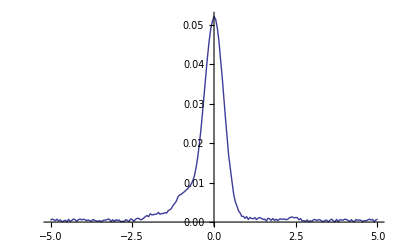

```mathematica
exweights={.10,.21,.57,.06,.06}^2; (*A^2 values, then plug in A values below*)
expositions={-1.8,-0.9,0,1.2,2.3};
ExampleCFn[x_]:=Table[gfn[Sqrt[exweights[[i]]],expositions[[i]],0.3,x],{i,1,Length[exweights]}]//Total
Print[ExampleCFn[x]]
ExampleCData=CenterAndNormalize@Table[{x,ExampleCFn[x]+0.005*RandomReal[]},{x,-5,5,0.05}];
ListLinePlot[ExampleCData,PlotRange->{{-5,5},All}]
```

Fitting this data is more difficult. We can again reproduce the qualitative features fairly well. However, the higher energy peaks are lost and the lower energy peaks are mixed together.

Sum of squares of residuals: 0.00001783641913286332

Weights | Means | σs
0.511879 | 0.0699241 | 0.264608
0.14623 | 0.00323053 | -3.69512
0.00118246 | 2.81243 | -0.00161987
0.10973 | -0.182463 | -0.212069
0.230979 | -0.530421 | -0.578339

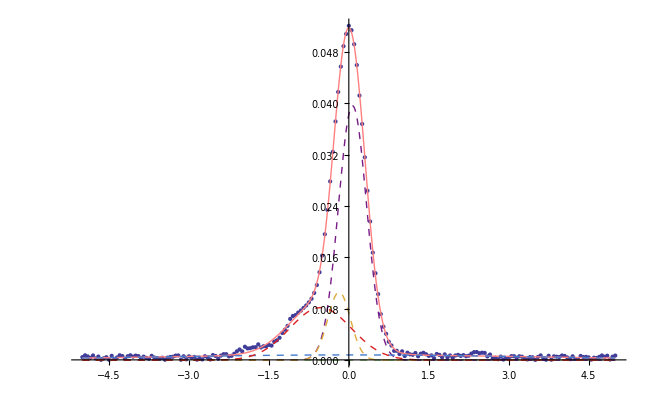

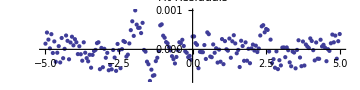

```mathematica
ExCModel=Model[ExampleCData,5];
FitSummary[ExampleCData,ExCModel];
```

Using the same parameters that were “good” before now yield obviously bad results.

Sum of squares of residuals: 0.0004053541797146091

Weights | Means | σs
0.0000954421 | -0.0155397 | 0.320131
0.00247895 | -68.7666 | 403.659
0.594509 | 55.9935 | 7.45767
0.402697 | -29.4027 | 1.73768
0.000219733 | 42.8074 | 4.27226

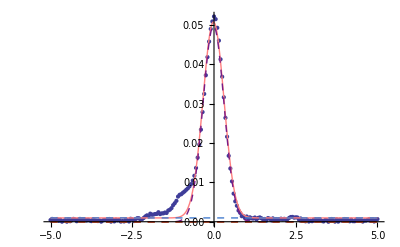

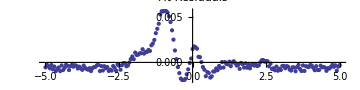

```mathematica
ExCModel=Model[ExampleCData,5,0.75];
FitSummary[ExampleCData,ExCModel];
```

Increasing the scaling factor slightly more does a good job of fitting the lower energy peaks, though the higher energy peaks are again lost.

Sum of squares of residuals: 9.264718679109545e-6

Weights | Means | σs
3.06036×10^-15 | -1.29625 | -1.11865
0.134998 | 0.238204 | -3.58036
0.0165686 | -1.79353 | -0.278683
0.747346 | 0.000203472 | -0.297975
0.101087 | -0.89592 | 0.302715

Sum of squares of residuals: 0.000011543754932814624

Weights | Means | σs
7.2399×10^-15 | -1.35234 | -0.988398
0.142498 | 0.276865 | -3.81384
0.0144225 | -1.8147 | -0.223026
0.736856 | 0.00274769 | -0.296621
0.106223 | -0.876587 | 0.327242

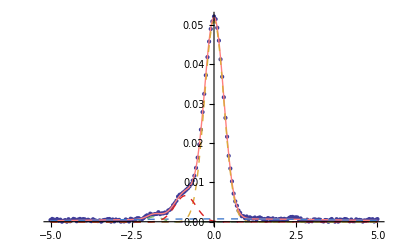

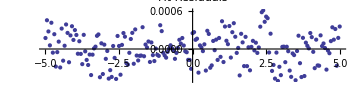

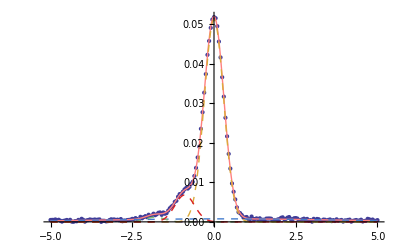

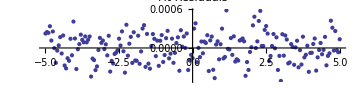

```mathematica
ExCModel=Model[ExampleCData,5,0.8];
FitSummary[ExampleCData,ExCModel];
```

Increasing the amount of noise makes fitting even more challenging. Try it!

### Example 5: Sample carbon 1s edge plus noise, using known peak locations

We saw before that fitting with noise was a bit challenging. Let’s look at that data again:

0.0036 ⅇ^(-5.55556 (-2.3+x)^2)+0.0036 ⅇ^(-5.55556 (-1.2+x)^2)+0.3249 ⅇ^(-5.55556 x^2)+0.0441 ⅇ^(-5.55556 (0.9+x)^2)+0.01 ⅇ^(-5.55556 (1.8+x)^2)

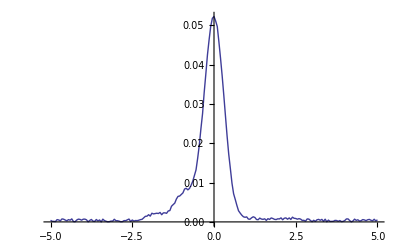

```mathematica
exweights={.10,.21,.57,.06,.06}^2; (*A^2 values, then plug in A values below*)
expositions={-1.8,-0.9,0,1.2,2.3};
ExampleCFn[x_]:=Table[gfn[Sqrt[exweights[[i]]],expositions[[i]],0.3,x],{i,1,Length[exweights]}]//Total
Print[ExampleCFn[x]]
ExampleCData=CenterAndNormalize@Table[{x,ExampleCFn[x]+0.005*RandomReal[]},{x,-5,5,0.05}];
ListLinePlot[ExampleCData,PlotRange->{{-5,5},All}]
```

Instead of fitting the data with completely free parameters, we can use known (or suspected) positions of the peaks using the FixedPeaksModel command. The default parameters do an abysmal job:

Sum of squares of residuals: 0.025720457482465334

Weights | σs
0.00625831 | -188.419
0.0000129541 | 452.965
0.0188394 | -8.22865
0.12559 | -175.531
0.849299 | 63.6919

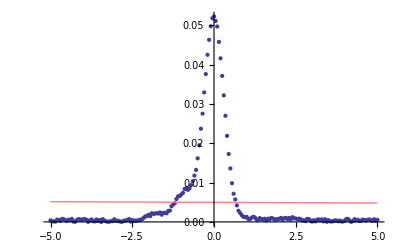

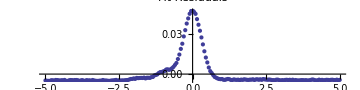

```mathematica
ExCModel=FixedPeaksModel[ExampleCData,expositions];
FitSummary[ExampleCData,ExCModel,True];
```

Again, reducing the scaling factor makes all the difference, although the high-energy peaks are still lost in the noise.

Sum of squares of residuals: 0.000012076621524929051

Weights | σs
0.0180364 | -0.231525
0.101678 | 0.309399
0.741997 | 0.29932
0.134124 | 4.8054
0.00416387 | -0.243033

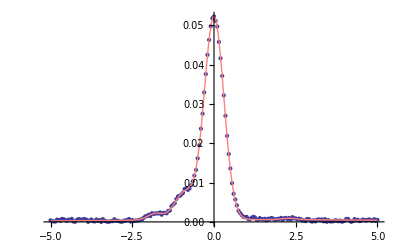

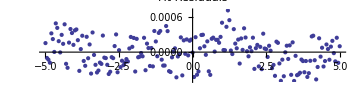

```mathematica
ExCModel=FixedPeaksModel[ExampleCData,expositions,0.6];
FitSummary[ExampleCData,ExCModel,True];
```

This result is somewhat robust against perturbations in the peak positions (in case we guess wrong). Here we change the peak positions by a random amount up to 10%. (Pushing this up to 20% makes the fit obviously bad in some cases.)

Sum of squares of residuals: 0.000015051389407066167

Weights | σs
0.013674 | 0.198344
0.119118 | 0.387661
0.675742 | 0.294312
0.177302 | 9.40811
0.0141639 | 0.822154

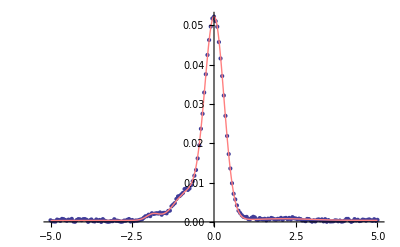

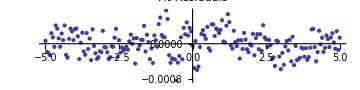

Sum of squares of residuals: 0.000013171652437168683

Weights | σs
0.0186807 | 0.245233
0.101868 | -0.3076
0.749343 | 0.298327
0.130109 | 3.91607
2.78301×10^-15 | 1.72366

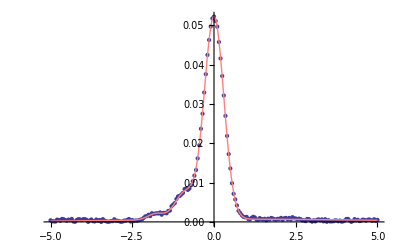

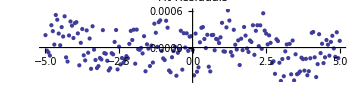

Sum of squares of residuals: 0.000013851429072773934

Weights | σs
0.0270929 | -0.35287
0.0869802 | 0.267963
0.756414 | -0.301338
0.129513 | 4.01282
1.02385×10^-14 | 3.88537

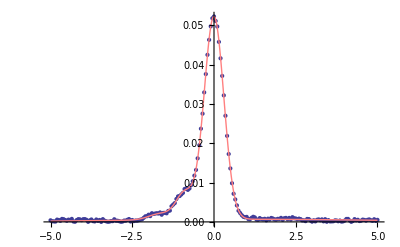

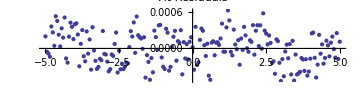

Sum of squares of residuals: 0.00003851970056768191

Weights | σs
0.105943 | 0.362202
0.748694 | 0.303574
0.141518 | -4.65368
0.00384489 | -0.285197
5.56024×10^-17 | -0.147655

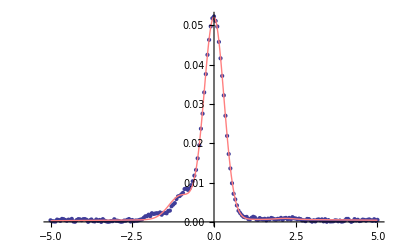

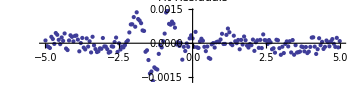

Sum of squares of residuals: 0.0000171243025320185

Weights | σs
0.0255355 | -0.36259
0.104334 | 0.320591
0.741246 | -0.295405
0.128885 | -3.90119
5.42657×10^-15 | 2.06799

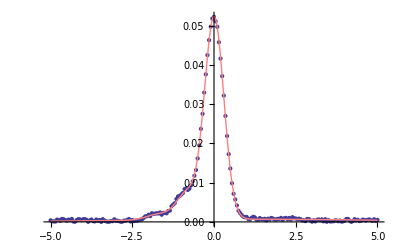

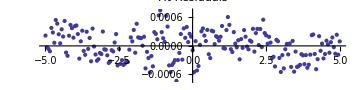

{Null,Null,Null,Null,Null}

```mathematica
Table[
ExCModel=FixedPeaksModel[ExampleCData,(#*RandomReal[{0.9,1.1}])&/@expositions,0.6];
FitSummary[ExampleCData,ExCModel,True];
,{i,1,5}
]
```

## Bulk fitting of actual XPS data

### Carbon Peak

#### Setup

```mathematica
RawCData=GetSpec[XPSPath,"Excel XPS","C1s"];
```

Removing sheets that do not contain the string "C1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

{C1s Scan J,C1s Scan I,C1s Scan H,C1s Scan G,C1s Scan F,C1s Scan E,C1s Scan D,C1s Scan C,C1s Scan B,C1s Scan A,C1s Scan}

11 spectra in all.

Importing Sheet C1s Scan J

Importing Sheet C1s Scan I

Importing Sheet C1s Scan H

Importing Sheet C1s Scan G

Importing Sheet C1s Scan F

Importing Sheet C1s Scan E

Importing Sheet C1s Scan D

Importing Sheet C1s Scan C

Importing Sheet C1s Scan B

Importing Sheet C1s Scan A

Importing Sheet C1s Scan

Formatting XPS Spectra

```mathematica
CSheets=GetSheets[XPSPath,"C1s"]
```

Removing sheets that do not contain the string "C1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

11 spectra in all.

{C1s Scan J,C1s Scan I,C1s Scan H,C1s Scan G,C1s Scan F,C1s Scan E,C1s Scan D,C1s Scan C,C1s Scan B,C1s Scan A,C1s Scan}

```mathematica
Ccoordlist=CoordInit[RawCData,285,8];
```

```mathematica
Ccoordlist
```

{{{285,1000},{281,1000},{289,1000},{283,1000}},{{285,1000},{281,1000},{289,1000},{283,1000}},{{285,1000},{281,1000},{289,1000},{283,1000}},{{285,1000},{281,1000},{289,1000},{283,1000}},{{285,1000},{281,1000},{289,1000},{283,1000}},{{285,1000},{281,1000},{289,1000},{283,1000}},{{285,1000},{281,1000},{289,1000},{283,1000}},{{285,1000},{281,1000},{289,1000},{283,1000}},{{285,1000},{281,1000},{289,1000},{283,1000}},{{285,1000},{281,1000},{289,1000},{283,1000}},{{285,1000},{281,1000},{289,1000},{283,1000}}}

```mathematica
PickGuesses[RawCData,Ccoordlist]
```

{,,,,,,,,,,}

```mathematica
CData=UserRemoveAve[RawCData,Ccoordlist];
```

```mathematica
CenteredCData=CenterAndNormalize/@CData;
```

#### Fitting with free parameters

```mathematica
AllCModels=Model[#,5]&/@CenteredCData;
```

Sum of squares of residuals: 0.000028966976204742832

Weights | Means | σs
1.08835×10^-19 | -3.61646 | -10.8387
0.414461 | -4.95955 | -0.0482086
0.0167343 | 1.66753 | 0.488546
0.284837 | 0.0405286 | 0.314208
0.283968 | -0.010976 | -0.58271

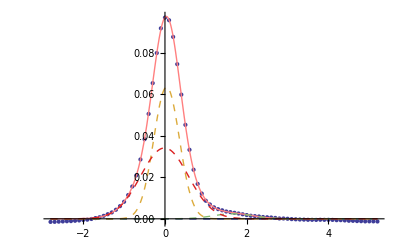

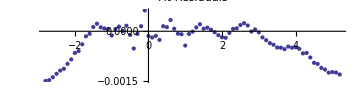

Sum of squares of residuals: 1.0456781366890188e-6

Weights | Means | σs
0.0365933 | 0.395833 | 0.250732
0.426242 | -0.0303126 | -0.307561
0.090115 | -1.62034 | 0.566118
0.167132 | 1.1903 | -1.54379
0.279918 | -0.0655884 | 0.606569

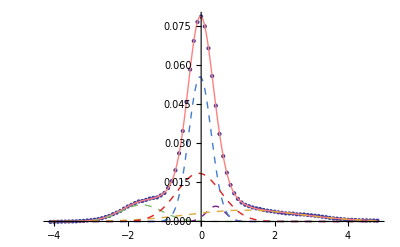

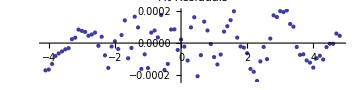

Sum of squares of residuals: 9.545186033491855e-7

Weights | Means | σs
0.604772 | 0.0295874 | 0.326211
0.0306261 | -0.0247673 | -0.183388
3.54706×10^-9 | -0.470814 | 1.05262
0.040082 | 2.39625 | 0.756061
0.32452 | -0.151579 | 0.906519

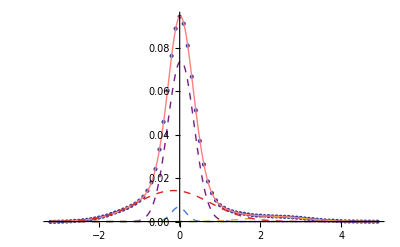

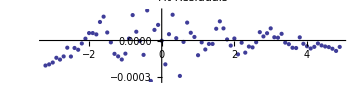

Sum of squares of residuals: 1.0238021202154226e-6

Weights | Means | σs
0.301393 | -0.108651 | 0.936899
0.593381 | -0.0336838 | -0.299416
0.0360858 | 2.40083 | 0.661489
0.0540995 | 0.391158 | 0.259377
0.0150411 | -0.642027 | 0.210327

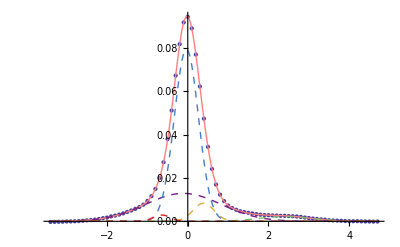

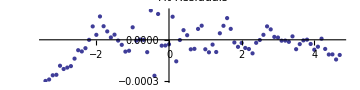

Sum of squares of residuals: 1.430657104191398e-6

Weights | Means | σs
0.191001 | 0.12545 | 0.988428
0.509971 | -0.0084128 | -0.31422
0.0494726 | 2.08639 | 1.39023
0.0264411 | 0.53896 | -0.238745
0.223114 | -0.296376 | 0.494524

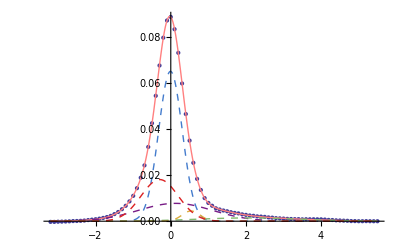

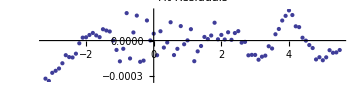

Sum of squares of residuals: 2.4975518343892955e-6

Weights | Means | σs
0.358247 | -0.220608 | 0.717043
2.04069×10^-13 | -3.8503 | 9.05136
4.00045×10^-14 | -4.34325 | -1.85626
0.10582 | 0.841083 | -1.4999
0.535933 | 0.0546657 | 0.314595

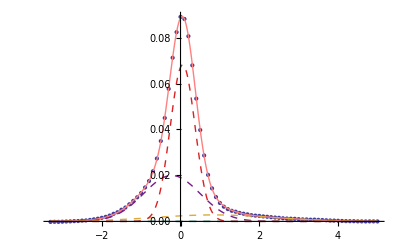

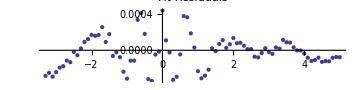

Sum of squares of residuals: 1.0163385325627944e-6

Weights | Means | σs
0.346665 | -0.198511 | -0.965293
0.0113008 | 0.582455 | 0.209161
0.0452292 | 2.44496 | 0.770885
0.595842 | 0.0199781 | -0.323724
0.000962256 | -0.186312 | 0.00543972

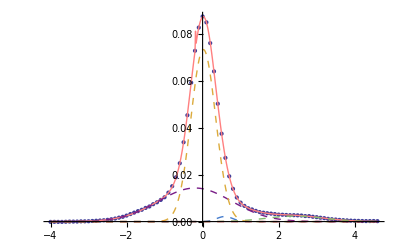

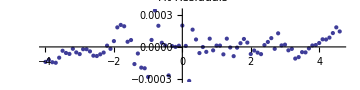

Sum of squares of residuals: 3.614213227071115e-6

Weights | Means | σs
0.31213 | 0.0489334 | 0.321519
0.0181814 | 2.51761 | -0.656035
0.501941 | 15.3199 | 2.77562
0.00195206 | 6.35092 | -0.0109505
0.165796 | -0.0770404 | -0.942357

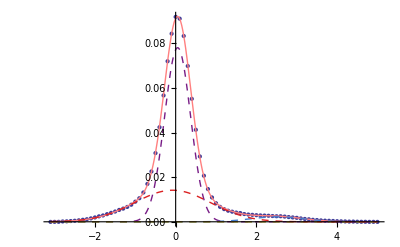

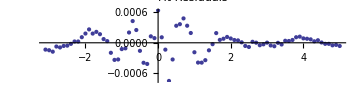

Sum of squares of residuals: 4.85993840513329e-6

Weights | Means | σs
0.0171219 | 2.4934 | -0.586224
0.448185 | -13.9961 | 1.93346
0.191449 | -0.168164 | -0.973343
0.342655 | -0.0320072 | -0.330831
0.000589446 | 5.70246 | -0.0510936

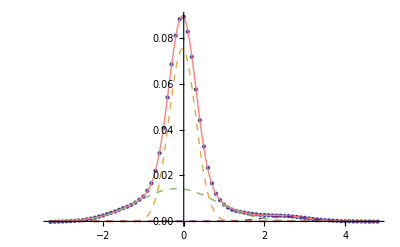

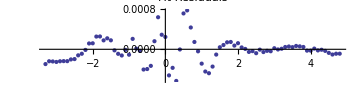

Sum of squares of residuals: 6.121535436805376e-7

Weights | Means | σs
0.0171819 | -1.69205 | 0.506762
0.300806 | -0.102373 | 0.813105
0.0616176 | 2.18603 | 0.91869
0.554038 | 0.0588654 | 0.33665
0.0663561 | 0.0120877 | -0.230367

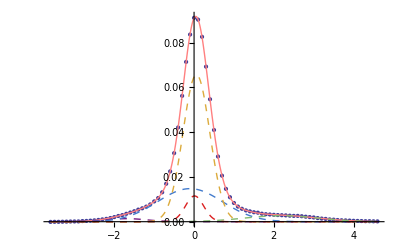

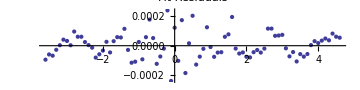

Sum of squares of residuals: 7.450476998557657e-6

Weights | Means | σs
0.600856 | 0.0323035 | 0.359858
0.0152927 | 2.6227 | 0.608607
0.0549959 | 15.2815 | 0.150735
0.328856 | -0.194137 | -1.21933
2.00443×10^-15 | -2.64942 | -0.494972

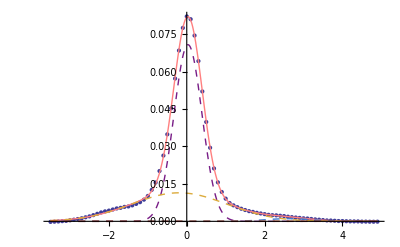

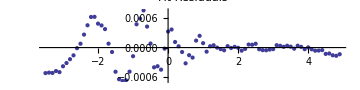

```mathematica
CSummaries=Table[FitSummary[CenteredCData[[x]],AllCModels[[x]]],{x,1,Length[CenteredCData],1}];
```

Visualize location of peaks and weights:

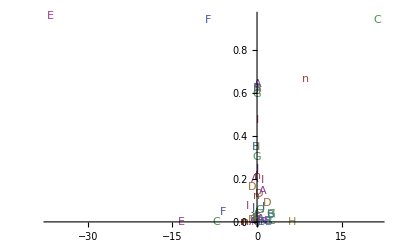

```mathematica
ComparePeaks[CSummaries,CSheets]
```

#### Fitting with fixed peak positions

Recall our literature peak positions:

```mathematica
expositions
```

{-1.8,-0.9,0,1.2,2.3}

```mathematica
AllCModels=FixedPeaksModel[#,{-1.7,-0.9,0,1.2,2.5},0.7]&/@CenteredCData;
```

Sum of squares of residuals: 0.00008657102936807372

Using fixed peaks analysis methods. μ -> 0.0319842

Weights | σs
3.81321×10^-16 | -2.68856
0.0538267 | -0.304762
0.878668 | -0.374748
0.0675056 | 0.562753
3.91654×10^-15 | 3.39945

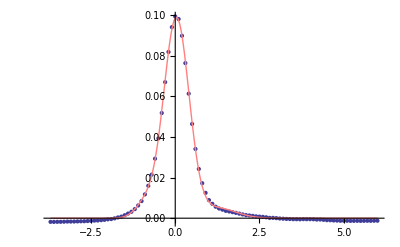

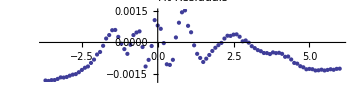

Sum of squares of residuals: 0.000023014541305969863

Using fixed peaks analysis methods. μ -> -0.00329637

Weights | σs
0.0921183 | 0.544554
0.0575306 | 0.399241
0.705958 | -0.373947
0.0693833 | 0.55724
0.0750095 | 1.27754

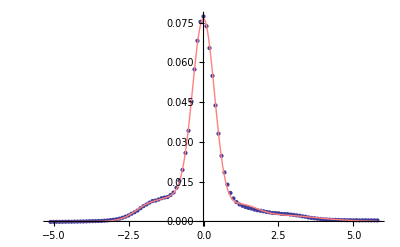

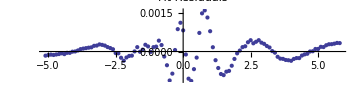

Sum of squares of residuals: 0.000032251998876458916

Using fixed peaks analysis methods. μ -> 0.0237749

Weights | σs
0.0308963 | -0.39152
0.0736233 | -0.341062
0.79991 | -0.344302
0.0695163 | -0.50077
0.0260544 | 0.464327

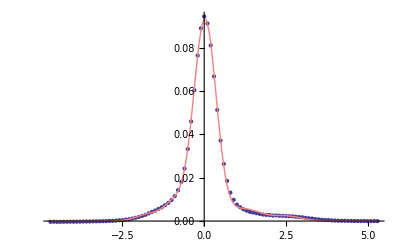

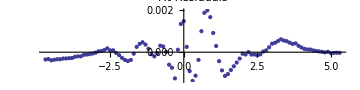

Sum of squares of residuals: 0.000011444887093180418

Using fixed peaks analysis methods. μ -> 0.893742

Weights | σs
0.133471 | 0.635698
0.757859 | 0.338271
0.053372 | 0.367625
0.0552978 | 0.78205
2.87226×10^-7 | 0.000288438

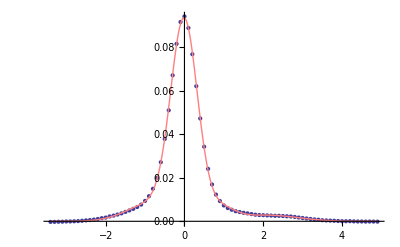

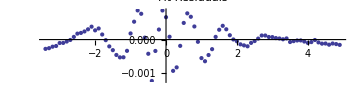

Sum of squares of residuals: 0.00001830485595323775

Using fixed peaks analysis methods. μ -> -0.0284674

Weights | σs
0.0122387 | -0.322884
0.064042 | 0.304941
0.815651 | -0.375336
0.0669715 | -0.5496
0.0410971 | 1.31979

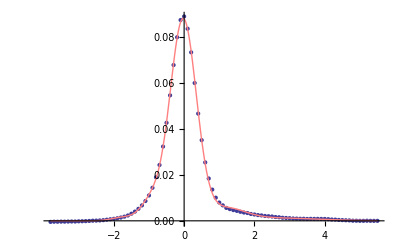

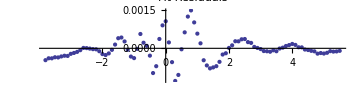

Sum of squares of residuals: 0.000013121818271362166

Using fixed peaks analysis methods. μ -> 0.954039

Weights | σs
0.183331 | -0.541911
0.717933 | 0.342372
0.0657243 | 0.427875
0.0262533 | 0.507412
0.0067583 | -0.411174

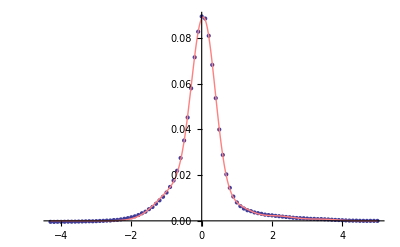

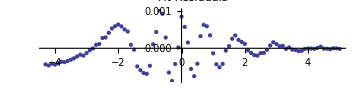

Sum of squares of residuals: 0.000023442611961686753

Using fixed peaks analysis methods. μ -> 0.0319589

Weights | σs
2.46288×10^-14 | 0.645968
0.163824 | 0.726102
0.736478 | -0.355901
0.0671566 | 0.492455
0.032541 | 0.509245

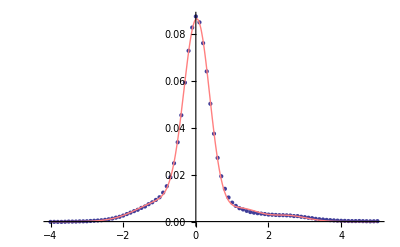

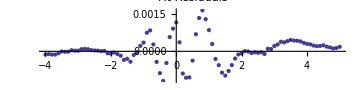

Sum of squares of residuals: 0.000027956091667237787

Using fixed peaks analysis methods. μ -> 0.0468746

Weights | σs
0.0315771 | 0.401363
0.0625786 | -0.337161
0.770826 | 0.347008
0.135019 | -1.08923
1.42434×10^-15 | 0.417358

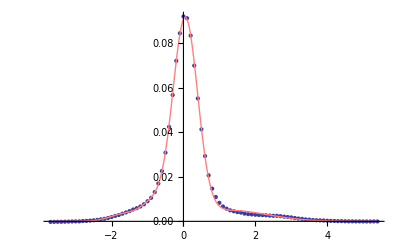

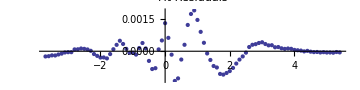

Sum of squares of residuals: 9.31666588232801e-6

Using fixed peaks analysis methods. μ -> 0.87373

Weights | σs
0.166365 | 0.719731
0.726727 | 0.347145
0.0507128 | 0.363752
0.0561948 | -0.799075
1.4787×10^-15 | -1.67746

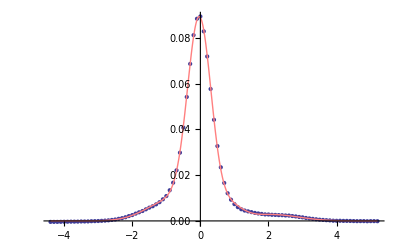

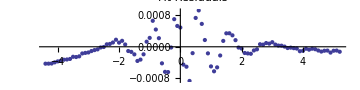

Sum of squares of residuals: 0.000025509989159125054

Using fixed peaks analysis methods. μ -> 0.0490727

Weights | σs
0.0357901 | 0.424909
0.0659859 | 0.336891
0.796683 | -0.351101
0.0708784 | -0.503949
0.0306622 | 0.489287

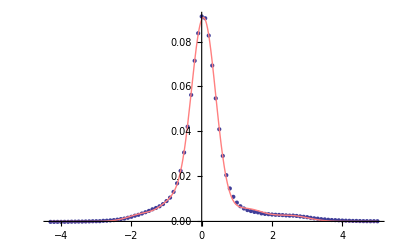

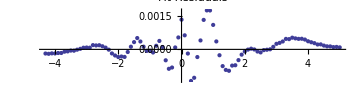

Sum of squares of residuals: 0.000010121628513431176

Using fixed peaks analysis methods. μ -> 0.933433

Weights | σs
0.203072 | -1.02432
0.66101 | 0.36657
0.131567 | -1.12616
3.30093×10^-13 | -2.4402
0.00435167 | -0.550096

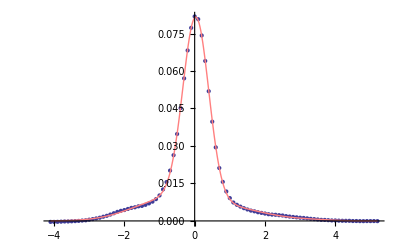

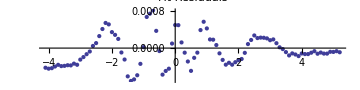

```mathematica
CSummaries=Table[FitSummary[CenteredCData[[x]],AllCModels[[x]],True],{x,1,Length[CenteredCData]}];
```

```mathematica
weights=Flatten/@(Reverse[Most[#ᵀ]]ᵀ&/@CSummaries)
```

{{3.81321×10^-16,0.0538267,0.878668,0.0675056,3.91654×10^-15},{0.0921183,0.0575306,0.705958,0.0693833,0.0750095},{0.0308963,0.0736233,0.79991,0.0695163,0.0260544},{0.133471,0.757859,0.053372,0.0552978,2.87226×10^-7},{0.0122387,0.064042,0.815651,0.0669715,0.0410971},{0.183331,0.717933,0.0657243,0.0262533,0.0067583},{2.46288×10^-14,0.163824,0.736478,0.0671566,0.032541},{0.0315771,0.0625786,0.770826,0.135019,1.42434×10^-15},{0.166365,0.726727,0.0507128,0.0561948,1.4787×10^-15},{0.0357901,0.0659859,0.796683,0.0708784,0.0306622},{0.203072,0.66101,0.131567,3.30093×10^-13,0.00435167}}

```mathematica
(μ->0.5)[[2]]
```

0.5

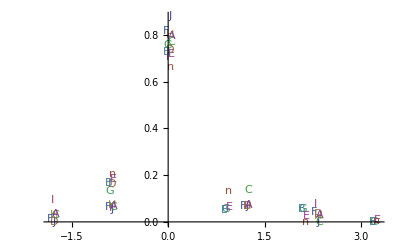

```mathematica
ComparePeaks[CSummaries,CSheets,expositions,AllCModels]
```

#### Fitting with free parameters, starting with informed guesses.

Instead of passing just the number of peaks, we can instead pass a list of guesses. See the last paragraph of the usage instructions:

```mathematica
?Model
```

Model[data,n] takes in a two-dimensional list data and a desired number of gaussians n and returns a nonlinear model for the data.
This is a difficult thing to do in general, so the function is tuned to fit the sort of data we usually get from the XPS. It works best if CenterAndNormalize has first been applied to the data. Sometimes additional tuning in the form of two optional arguments (the Scaling Factor sf and the Crossing Probability cp) can be helpful.
Instead of a desired number of gaussians, a list of guesses can be passed to the function in the format {{Weight 1, Mean 1, σ 1}, {Weight 1, Mean 1, σ 2}, ..., {Weight n, Mean n, σ n}}. In this case, the function will automatically detect that you're passing it a guess and start fitting around these parameters. In this case, the search space can be reduced by reducing sf.

Recall our list of positions and define a list of guesses.

```mathematica
expositions
```

{-1.8,-0.9,0,1.2,2.3}

```mathematica
guesses={{0.1,-1.8,0.5},{0.1,-0.9,0.5},{0.25,0,0.5},{0.05,1.2,0.5},{0.05,2.3,0.5}};
```

```mathematica
AllCModels=Model[#,2,"v",0.55]&/@CenteredCData;
```

NMinimize::nnum: The function value TagBox[Experimental`NumericalFunction[{Hold[« 1 »], Block}, {0, {{{}, 1, 0, Hold[0.06174363185130221`], 0, 0}, {{}, 1, 1, Hold[-1.589931947840198`], 0, 0}, {{}, 1, 2, Hold[0.`], 0, 0}, {{}, 1, 3, Hold[0.`], 0, 0}, {{}, 1, 4, Hold[0.30303144997090536`], 0, 0}, {{}, 1, 5, Hold[-0.008423566682984142`], 0, 0}, {{}, 1, 6, Hold[0.3243282237267163`], 0, 0}, {{}, 1, 7, Hold[0.1514330453887688`], 0, 0}}}, {{{1, 8, 817}, {{{Hold[Block[{« 4 »}, CompoundExpression[« 3 »]]], Block}, « 3 », Automatic}, « 1 »}}}, « 1 », {908, MachinePrecision, « 4 », Automatic, None}, {None, None, None}], False, Rule[Editable, False]] is not a number at {A[1], A[2], δ[1], δ[2], μ[1], μ[2], σ[1], σ[2]} = {0.0617436, 0.303031, 0., 0.151433, -1.58993, -0.00842357, 0., 0.324328}.

NMinimize::nnum: The function value TagBox[Experimental`NumericalFunction[{Hold[« 1 »], Block}, {0, {{{}, 1, 0, Hold[0.`], 0, 0}, {{}, 1, 1, Hold[17.282725577497168`], 0, 0}, {{}, 1, 2, Hold[0.`], 0, 0}, {{}, 1, 3, Hold[0.`], 0, 0}, {{}, 1, 4, Hold[0.3226493849801013`], 0, 0}, {{}, 1, 5, Hold[0.0153140471530368`], 0, 0}, {{}, 1, 6, Hold[0.3147568080372557`], 0, 0}, {{}, 1, 7, Hold[0.09883035817844148`], 0, 0}}}, {{{1, 8, 817}, {{{Hold[Block[{« 4 »}, CompoundExpression[« 3 »]]], Block}, Automatic, None, 1, Automatic}, {« 1 »}}}}, {8, « 3 »}, {908, MachinePrecision, « 4 », Automatic, None}, {None, None, None}], False, Rule[Editable, False]] is not a number at {A[1], A[2], δ[1], δ[2], μ[1], μ[2], σ[1], σ[2]} = {0., 0.322649, 0., 0.0988304, 17.2827, 0.015314, 0., 0.314757}.

NMinimize::nnum: The function value TagBox[Experimental`NumericalFunction[« 1 »], False, Rule[Editable, False]] is not a number at {A[1], A[2], δ[1], δ[2], μ[1], μ[2], σ[1], σ[2]} = {0., 0.319822, 0., 0.124996, 34.4167, -0.0177315, 0., 0.302164}.

General::stop: Further output of NMinimize :: nnum will be suppressed during this calculation.

Sum of squares of residuals (as percent of total): 0.06817671412425425

A | μ | σ | δ
0.000297536 | 14.9199 | 1.07755 | 22.9241
0.999702 | 0.0281384 | 0.314636 | 0.157341

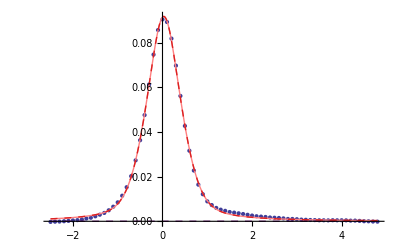

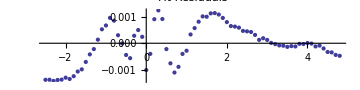

Sum of squares of residuals (as percent of total): 0.3200278117334533

A | μ | σ | δ
0.0410318 | -1.18189 | 0.257325 | 2.05839
0.958968 | -0.0118165 | 0.378378 | 0.0608827

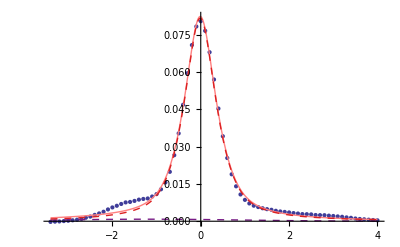

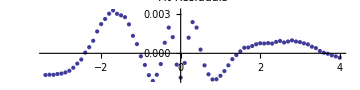

Sum of squares of residuals (as percent of total): 0.10603177830868184

A | μ | σ | δ
0.941868 | 0.0148143 | 0.312016 | 0.102327
0.0581316 | 7.67526 | 1.66866 | 11.2242

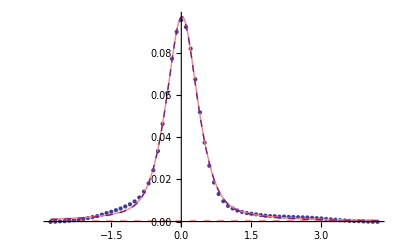

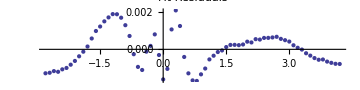

Sum of squares of residuals (as percent of total): 0.08222053724683483

A | μ | σ | δ
0.981283 | -0.0185402 | 0.315035 | 0.109575
0.0187172 | 2.28009 | 0.375845 | 1.42505

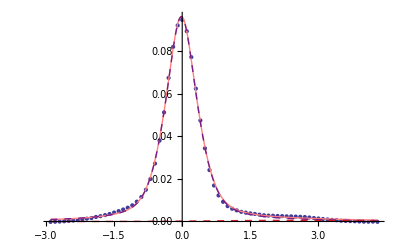

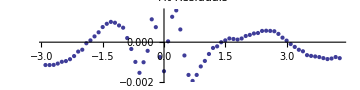

Sum of squares of residuals (as percent of total): 0.07905034048762696

A | μ | σ | δ
0.0102155 | 1.31034 | 0.744374 | 5.06763×10^-8
0.989785 | -0.0356747 | 0.323367 | 0.142338

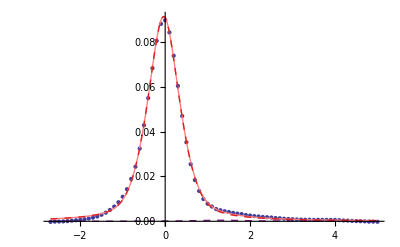

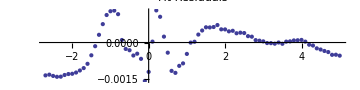

Sum of squares of residuals (as percent of total): 0.24448067901762707

A | μ | σ | δ
0.0383077 | -0.253529 | 0.81357 | 0.199046
0.961692 | 0.022118 | 0.334692 | 0.108975

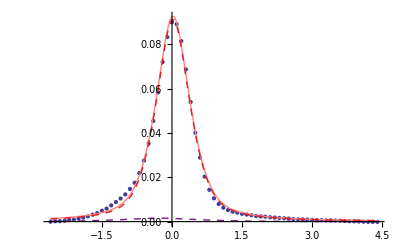

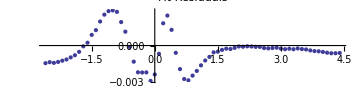

Sum of squares of residuals (as percent of total): 0.16270968600933353

A | μ | σ | δ
0.849733 | 0.014371 | 0.337339 | 0.0975698
0.150267 | 6.24664 | 2.06139 | 26.8193

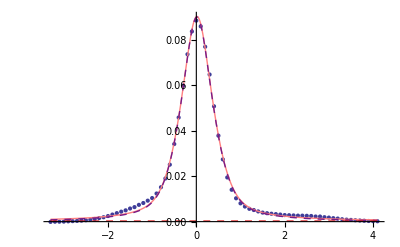

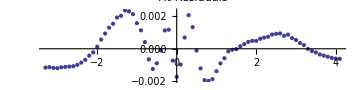

Sum of squares of residuals (as percent of total): 0.11175021128449311

A | μ | σ | δ
0.0211653 | 5.43865 | 0.547024 | 5.24373
0.978835 | 0.0428503 | 0.313797 | 0.11185

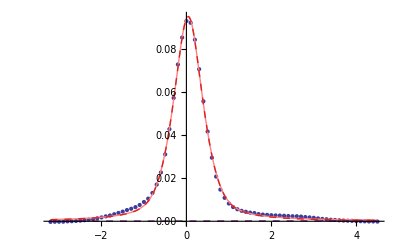

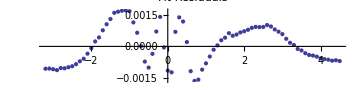

Sum of squares of residuals (as percent of total): 0.11122867479319834

A | μ | σ | δ
0.983506 | -0.039951 | 0.330285 | 0.108564
0.0164941 | -0.918535 | 0.59626 | 0.711352

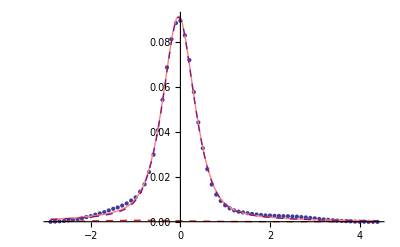

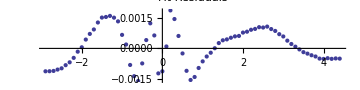

Sum of squares of residuals (as percent of total): 0.10865741190303924

A | μ | σ | δ
0.109254 | 9.99478 | 3.21805 | 7.09178
0.890746 | 0.042541 | 0.320058 | 0.099254

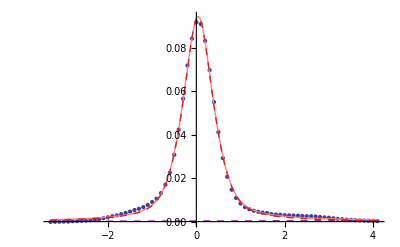

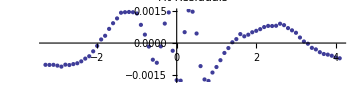

Sum of squares of residuals (as percent of total): 0.16810017298781688

A | μ | σ | δ
0.875587 | 0.0233899 | 0.356118 | 0.108135
0.124413 | -11.5014 | 0.247431 | 14.3489

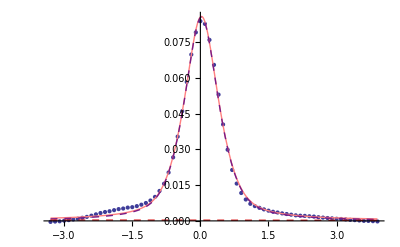

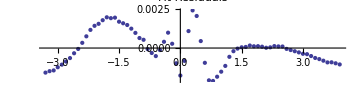

```mathematica
CSummaries=Table[FitSummary[CenteredCData[[x]],AllCModels[[x]],"v"],{x,1,Length[CenteredCData],1}];
```

Visualize location of peaks and weights:

```mathematica
ComparePeaks[CSummaries,CSheets]
```

-Graphics-

### Oxygen Peak

#### Setup

```mathematica
RawOData=GetSpec[XPSPath,"Excel XPS","O1s"];
```

Removing sheets that do not contain the string "O1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

{O1s Scan J,O1s Scan I,O1s Scan H,O1s Scan G,O1s Scan F,O1s Scan E,O1s Scan D,O1s Scan C,O1s Scan B,O1s Scan A,O1s Scan}

11 spectra in all.

Importing Sheet O1s Scan J

Importing Sheet O1s Scan I

Importing Sheet O1s Scan H

Importing Sheet O1s Scan G

Importing Sheet O1s Scan F

Importing Sheet O1s Scan E

Importing Sheet O1s Scan D

Importing Sheet O1s Scan C

Importing Sheet O1s Scan B

Importing Sheet O1s Scan A

Importing Sheet O1s Scan

Formatting XPS Spectra

```mathematica
OSheets=GetSheets[XPSPath,"O1s"]
```

Removing sheets that do not contain the string "O1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

11 spectra in all.

{O1s Scan J,O1s Scan I,O1s Scan H,O1s Scan G,O1s Scan F,O1s Scan E,O1s Scan D,O1s Scan C,O1s Scan B,O1s Scan A,O1s Scan}

```mathematica
Ocoordlist=CoordInit[RawOData,532.5,7,12000]
```

{{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}}}

```mathematica
PickGuesses[RawOData,Ocoordlist]
```

Part::partw: Part 2 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 3 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 4 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{,,,,,,,,,,}

```mathematica
OData=UserRemoveAve[RawOData,Ocoordlist];
```

```mathematica
CenteredOData=CenterAndNormalize/@OData;
```

#### Fitting with free parameters

Fitting works better if the fitting parameters are tweaked a little.

```mathematica
AllOModels=Model[#,4,0.7,0.1]&/@CenteredOData;
```

Weights | Means | σs
0.874396 | 0. | -0.742735
0.118266 | 1.46439 | 0.505756
0.00733787 | 0.730778 | 0.202887
2.38909×10^-15 | 1.22805 | -0.0557857

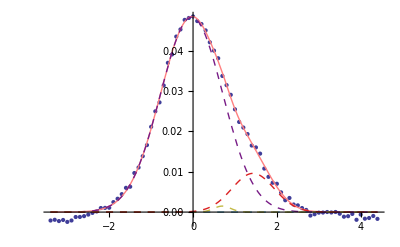

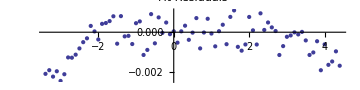

Weights | Means | σs
0.837196 | 0. | 0.828332
0.125163 | -1.26161 | 0.513958
0.0376415 | -2.2437 | -0.524787
1.09389×10^-15 | 7.28843 | 1.13965

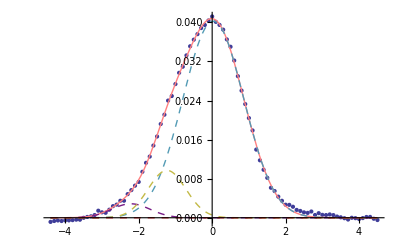

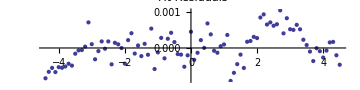

Weights | Means | σs
0.653603 | 0. | -0.884188
0.346397 | 0.357317 | -0.52724
1.05667×10^-15 | 2.5096 | 0.766575
7.45861×10^-16 | -0.23765 | 0.512961

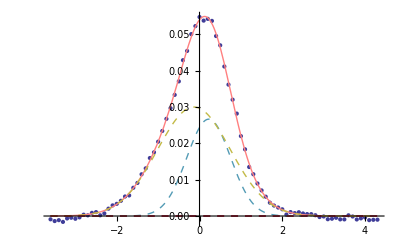

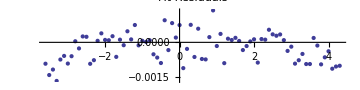

Weights | Means | σs
0.776322 | 0. | -0.873546
0.209321 | 0.324272 | -0.453076
0.0110191 | -2.00676 | -0.375741
0.00333731 | 0.990021 | 0.0838162

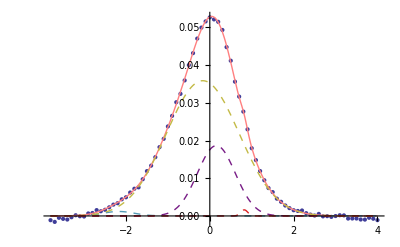

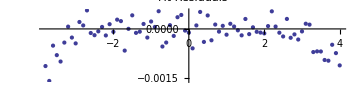

Weights | Means | σs
0.534729 | 0. | 0.941181
0.348729 | 4.44663 | -0.111634
0.116542 | -0.561733 | -0.540562
7.39575×10^-14 | -1.26733 | -1.66903

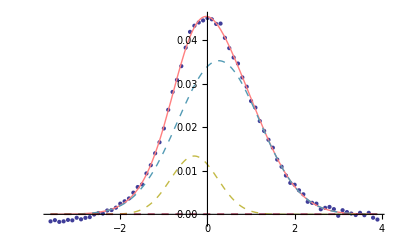

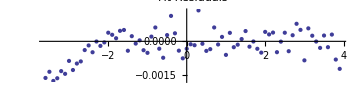

Weights | Means | σs
0.973399 | 0. | -0.879313
0.0192061 | 0.423804 | 0.40934
0.0073945 | -1.88311 | 0.30123
2.87036×10^-15 | -3.6756 | 2.07797

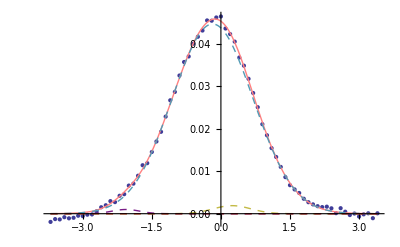

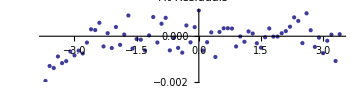

Weights | Means | σs
0.773084 | 0. | -0.923937
0.213826 | 0.413824 | 0.482582
0.00824337 | -2.26355 | -0.406699
0.00484642 | 2.62401 | -0.40358

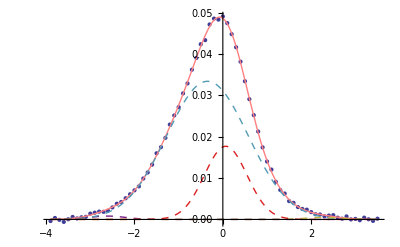

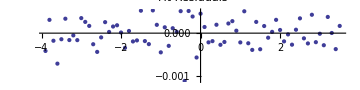

Weights | Means | σs
0.852568 | 0. | -0.806482
0.0785695 | 0.273038 | 0.385294
0.0688621 | -1.58587 | 0.637021
2.53352×10^-11 | -1.22528 | 1.09366

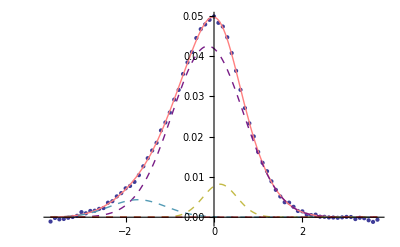

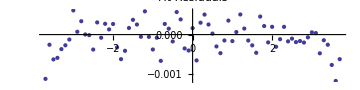

Weights | Means | σs
0.702948 | 0. | -0.919186
0.291838 | 0.446328 | 0.551286
0.00336372 | 0.48207 | -0.0744654
0.00184975 | -0.0628031 | 0.0283305

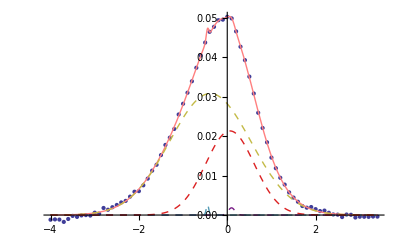

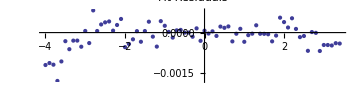

Weights | Means | σs
0.888669 | 0. | -0.722229
0.0680254 | -1.84434 | 0.530839
0.043306 | -1.19196 | 0.345794
1.55702×10^-15 | -0.987686 | -1.7759

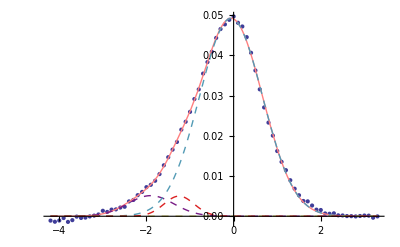

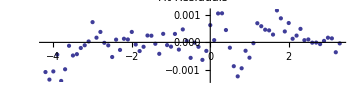

Weights | Means | σs
0.841105 | 0. | 0.969829
0.151044 | 0.784281 | -0.489246
0.0078509 | -2.1727 | -0.36118
4.66842×10^-14 | 0.20277 | -0.484569

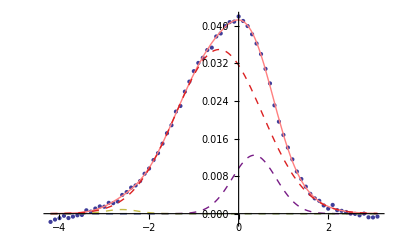

-Graphics-

```mathematica
OSummaries=Table[FitSummary[CenteredOData[[x]],AllOModels[[x]]],{x,1,Length[CenteredOData]}];
```

Visualize location of peaks and weights:

```mathematica
ComparePeaks[OSummaries,OSheets]
```

-Graphics-

#### Fitting with fixed peak positions

Fitting works better if the fitting parameters are tweaked a little.

```mathematica
AllOModels=Model[#,4,0.7,0.1]&/@CenteredOData;
```

```mathematica
OSummaries=Table[FitSummary[CenteredOData[[x]],AllOModels[[x]]],{x,1,Length[CenteredOData]}];
```

Weights | Means | σs
0.874396 | 0. | -0.742735
0.118266 | 1.46439 | 0.505756
0.00733787 | 0.730778 | 0.202887
2.38909×10^-15 | 1.22805 | -0.0557857

-Graphics-

-Graphics-

Weights | Means | σs
0.837196 | 0. | 0.828332
0.125163 | -1.26161 | 0.513958
0.0376415 | -2.2437 | -0.524787
1.09389×10^-15 | 7.28843 | 1.13965

-Graphics-

-Graphics-

Weights | Means | σs
0.653603 | 0. | -0.884188
0.346397 | 0.357317 | -0.52724
1.05667×10^-15 | 2.5096 | 0.766575
7.45861×10^-16 | -0.23765 | 0.512961

-Graphics-

-Graphics-

Weights | Means | σs
0.776322 | 0. | -0.873546
0.209321 | 0.324272 | -0.453076
0.0110191 | -2.00676 | -0.375741
0.00333731 | 0.990021 | 0.0838162

-Graphics-

-Graphics-

Weights | Means | σs
0.534729 | 0. | 0.941181
0.348729 | 4.44663 | -0.111634
0.116542 | -0.561733 | -0.540562
7.39575×10^-14 | -1.26733 | -1.66903

-Graphics-

-Graphics-

Weights | Means | σs
0.973399 | 0. | -0.879313
0.0192061 | 0.423804 | 0.40934
0.0073945 | -1.88311 | 0.30123
2.87036×10^-15 | -3.6756 | 2.07797

-Graphics-

-Graphics-

Weights | Means | σs
0.773084 | 0. | -0.923937
0.213826 | 0.413824 | 0.482582
0.00824337 | -2.26355 | -0.406699
0.00484642 | 2.62401 | -0.40358

-Graphics-

-Graphics-

Weights | Means | σs
0.852568 | 0. | -0.806482
0.0785695 | 0.273038 | 0.385294
0.0688621 | -1.58587 | 0.637021
2.53352×10^-11 | -1.22528 | 1.09366

-Graphics-

-Graphics-

Weights | Means | σs
0.702948 | 0. | -0.919186
0.291838 | 0.446328 | 0.551286
0.00336372 | 0.48207 | -0.0744654
0.00184975 | -0.0628031 | 0.0283305

-Graphics-

-Graphics-

Weights | Means | σs
0.888669 | 0. | -0.722229
0.0680254 | -1.84434 | 0.530839
0.043306 | -1.19196 | 0.345794
1.55702×10^-15 | -0.987686 | -1.7759

-Graphics-

-Graphics-

Weights | Means | σs
0.841105 | 0. | 0.969829
0.151044 | 0.784281 | -0.489246
0.0078509 | -2.1727 | -0.36118
4.66842×10^-14 | 0.20277 | -0.484569

-Graphics-

-Graphics-

Visualize location of peaks and weights:

```mathematica
ComparePeaks[OSummaries,OSheets]
```

-Graphics-